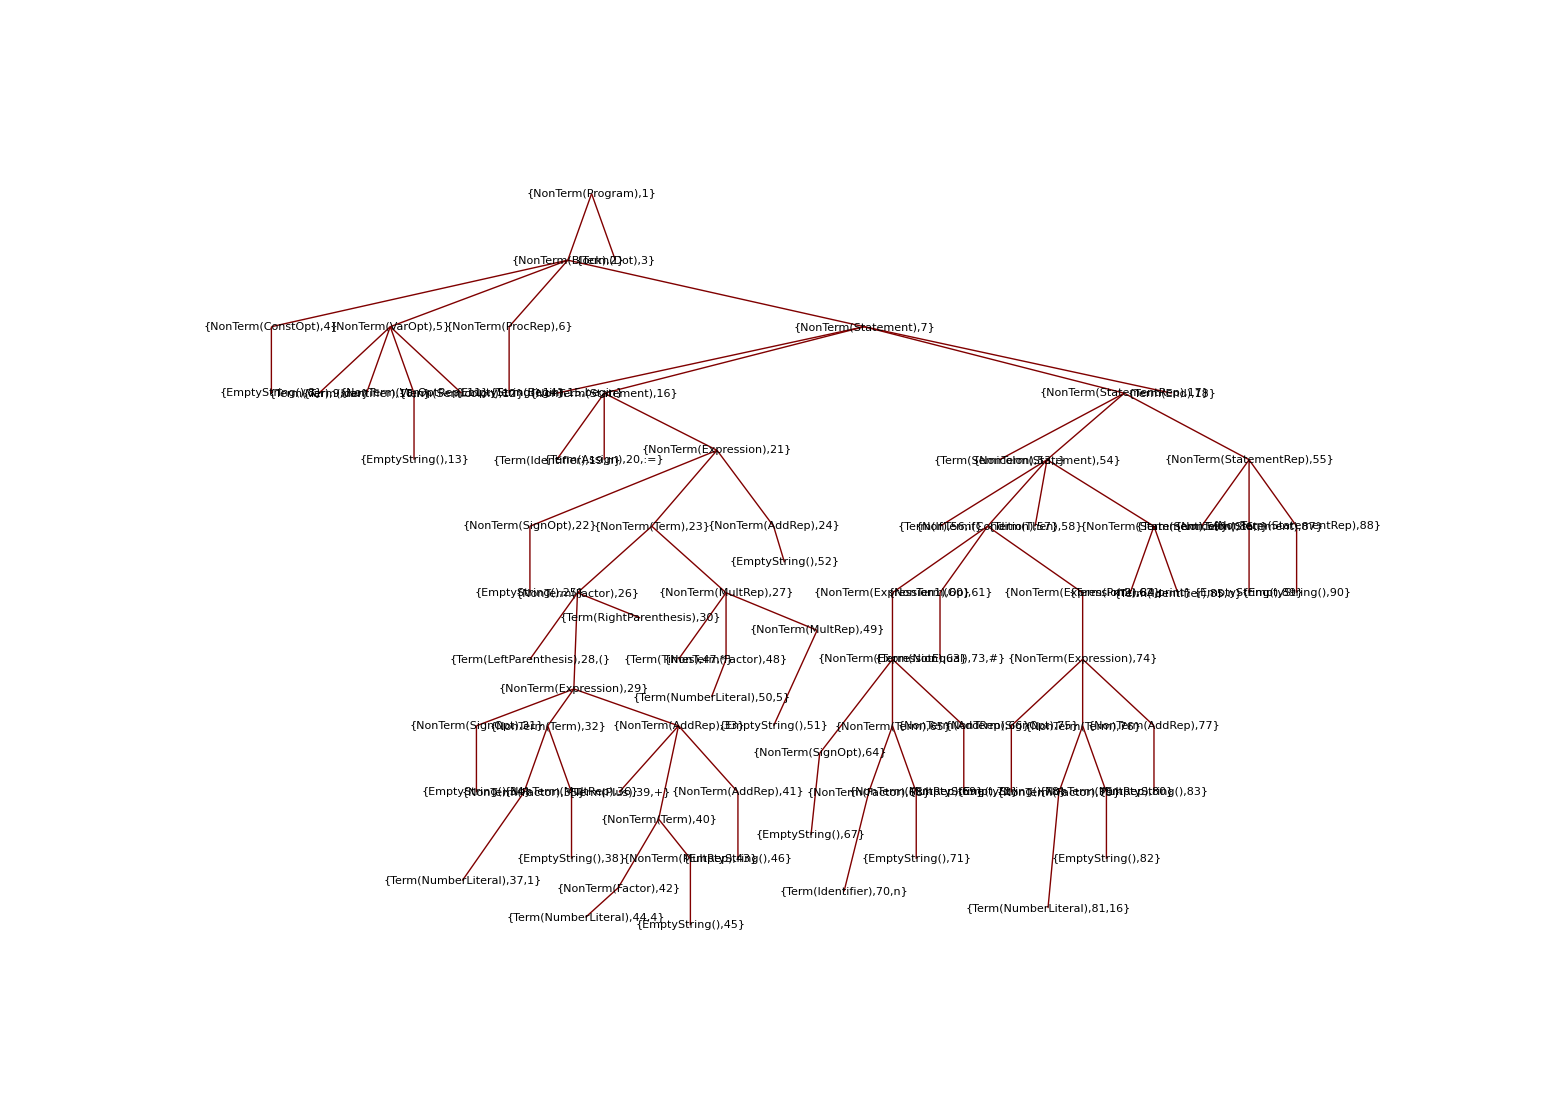

```mathematica
tinyProgram =
"procedure p1;
var n, f;
begin
   n := 0;
   f := 1;
   while n # 16 do
   begin
      n := n + 1;
      f := f * n;
   end;
end;

procedure p2;
var n;
begin
   n := (1+4)*5;
   if n # 16 then
   begin
      print n;
   end;
end;

begin
    call p1;
    call p2;
end.
";
```

```mathematica
tokens = Tokenize[tinyProgram,symbolTokens,keywordDFA];
```

```mathematica
parseTree = Parse[tokens,grammar] ;
{NonTerm["Program"],1}["TACode"]/.SynthesizeTree[parseTree]
```

begin_proc p1
declare_var n
declare_var f
set n 0
set f 1
label L1$3
not_equal n 16 $0
if_false $0 goto L2$3
add n 1 $1
set n $1
multiply f n $2
set f $2
goto L1$3
label L2$3
end_proc p1
begin_proc p2
declare_var n
add 1 4 $4
multiply $4 5 $5
set n $5
not_equal n 16 $6
if_false $6 goto L$7
print n
label L$7
end_proc p2
call p1
call p2
halt